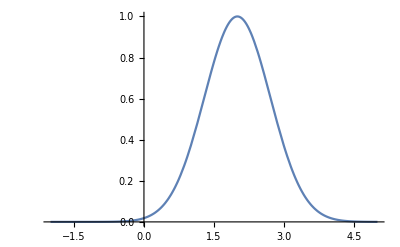

1.77245

1.7724539

```mathematica
f[x_]:=Exp[-(x-a)^2];                                                    (*Not normalized*)
a=2;
Plot[f[x],{x,-2,5},PlotRange->Full,PlotLegends->"Expressions"]
NIntegrate[f[x],{x,-∞,∞}]                                                                                                (*Area under Exp[-(x-a)^2] is √π *)
N[Sqrt[Pi],8]
```

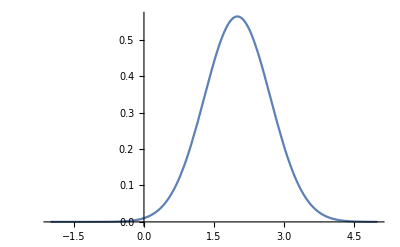

1.

```mathematica
f[x_]:=(1/Sqrt[π])*Exp[-(x-a)^2];                        (*Normalized*)
a=2;
Plot[f[x],{x,-2,5},PlotRange->Full,PlotLegends->"Expressions"]
NIntegrate[f[x],{x,-∞,∞}]
```

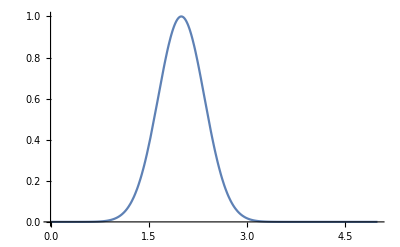

0.886227

1.77245

```mathematica
f[x_,k_]:=Exp[-((x-a)^2)/k^2];                                     (*Not normalized*) (*What do k do in the exponential*)
a=2;
Plot[f[x,k=0.5],{x,0,5},PlotRange->Full,PlotLegends->"Expressions"]
NIntegrate[f[x,k=0.5],{x,-∞,∞}]
2*NIntegrate[f[x,k=0.5],{x,-∞,∞}]
```

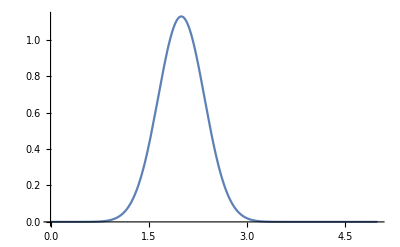

1.

1.

```mathematica
f[x_,k_]:=(1/(k Sqrt[π]))Exp[-((x-a)^2)/k^2];                         (*Normalized*)
a=2;
Plot[f[x,k=0.5],{x,0,5},PlotRange->Full,PlotLegends->"Expressions"]
NIntegrate[f[x,k=0.5],{x,-∞,∞}]
NIntegrate[f[x,k=0.05],{x,-∞,∞}]
```

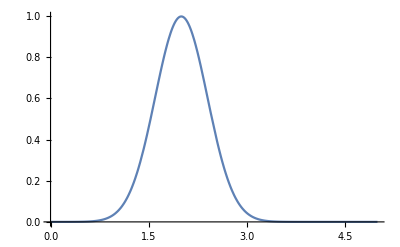

```mathematica
G[x_]:=(1/(σ*Sqrt[2Pi]))Exp[-((x-a)^2)/(2σ^2)];         (*What do σ do in the exponenetial*)
a=2;σ=0.4;
Plot[G[x], {x, 0,5}]
```

General::munfl: Exp[-799.918] is too small to represent as a normalized machine number; precision may be lost.

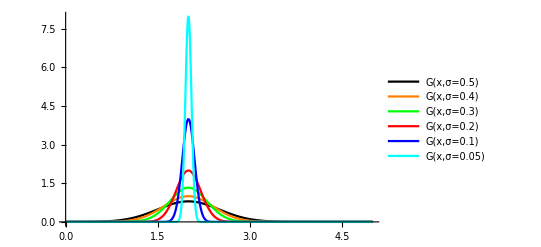

1.

1.

```mathematica
G[x_, σ_]:=(1/(σ*Sqrt[2Pi]))Exp[-((x-a)^2)/(2σ^2)];     (*What do σ do in the exponenetial*)
a=2;
Plot[{G[x, σ=0.5],G[x, σ=0.4],G[x, σ=0.3],G[x, σ=0.2],G[x, σ=0.1],G[x, σ=0.05]},{x, 0,5}, PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan}, PlotLegends->"Expressions"]
NIntegrate[G[x,σ=0.5],{x,-∞, ∞}]
NIntegrate[G[x,σ=0.05],{x,-∞, ∞}]
```

```mathematica
G2[x_,y_,σ_]:=(1/((σ^2)*2Pi))Exp[-(((x-a)^2)+((y-b)^2))/(2σ^2)];
a=2;b=3;
Plot3D[G2[x,y,σ=0.1], {x, 0,3},{y,0,4},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
G2[x_,y_,σ_]:=(1/((σ^2)*2Pi))Exp[-(((x-a)^2)+((y-b)^2))/(2σ^2)];
a=2;b=3;
Plot3D[{G2[x,y,σ=0.4],G2[x,y,σ=0.3],G2[x,y,σ=0.2],G2[x,y,σ=0.1]}, {x, 0,3},{y,0,4},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"},PlotStyle->{Red,Green,Orange,Blue,Opacity[0.3]}]
```

-Graphics3D-

```mathematica
g2[x_,y_]:=Exp[-((x^2)+(y^2))];
Plot3D[g2[x,y], {x, -3,3},{y,-3,3},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
g2[x_,y_]:=Exp[-x^2]+Exp[-y^2];
Plot3D[g2[x,y], {x, -5,5},{y,-5,5},PlotPoints->100,PlotRange->Full,AxesLabel->{"x","y"},ColorFunction->"Rainbow"]
```

-Graphics3D-

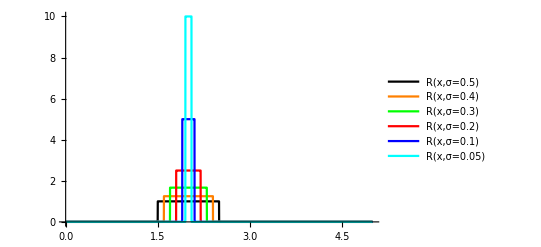

1.

1.

```mathematica
R[x_,σ_]:=Piecewise[{{1/(2σ),-σ<x-a<σ},{0,Modulus[x-a]>σ}}];                  (*Rectangular function*)
a=2;
Plot[{R[x,σ=0.5],R[x,σ=0.4],R[x,σ=0.3],R[x,σ=0.2],R[x,σ=0.1],R[x,σ=0.05]},{x,0,5},PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan},PlotLegends->"Expressions"]
NIntegrate[R[x,σ=0.5],{x,-∞, ∞}]
NIntegrate[R[x,σ=0.05],{x,-∞, ∞}]
```

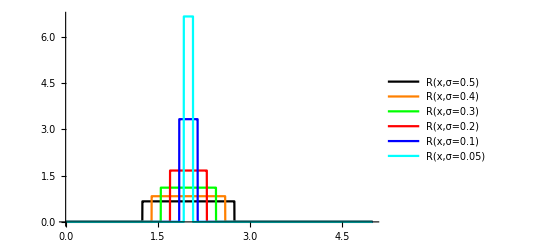

1.

1.

```mathematica
R[x_,σ_]:=Piecewise[{{1/(3σ),-3σ/2<x-a<3σ/2},{0,Modulus[x-a]>3σ/2}}];
a=2;
Plot[{R[x,σ=0.5],R[x,σ=0.4],R[x,σ=0.3],R[x,σ=0.2],R[x,σ=0.1],R[x,σ=0.05]},{x,0,5},PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan},PlotLegends->"Expressions"]
NIntegrate[R[x,σ=0.5],{x,-∞, ∞}]
NIntegrate[R[x,σ=0.05],{x,-∞, ∞}]
```

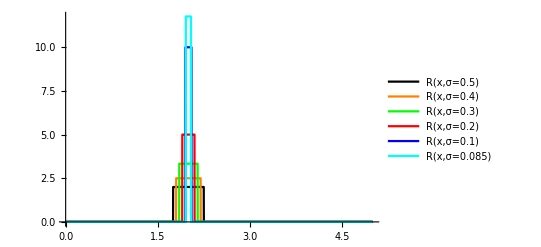

1.

1.

```mathematica
R[x_,σ_]:=Piecewise[{{1/σ,-σ/2<x-a<σ/2},{0,Modulus[x-a]>σ/2}}];
a=2;
Plot[{R[x,σ=0.5],R[x,σ=0.4],R[x,σ=0.3],R[x,σ=0.2],R[x,σ=0.1],R[x,σ=0.085]},{x,0,5},PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan},PlotLegends->"Expressions"]
NIntegrate[R[x,σ=0.5],{x,-∞, ∞}]
NIntegrate[R[x,σ=0.05],{x,-∞, ∞}]
```

g/π

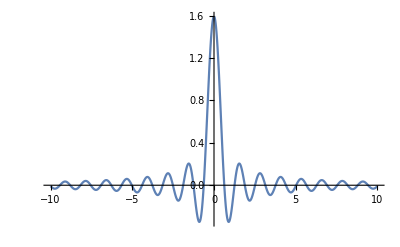

```mathematica
s[x_]:=Sin[g x]/(π x);
Limit[s[x],x->0]
g=5;
Plot[s[x],{x,-10,10},PlotRange->Full]
```

1

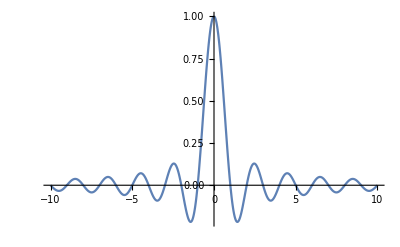

```mathematica
s[x_]:=Sin[π x]/(π x);
Limit[s[x],x->0]
Plot[s[x],{x,-10,10},PlotRange->Full]
```

```mathematica
s[x_,y_]:=(Sin[g x]/(π x))(Sin[g y]/(π y));
Limit[s[x],x->0]
g=25;
Plot3D[s[x,y],{x,-1,1},{y,-1,1},PlotPoints->100,PlotRange->Full,ColorFunction->"TemperatureMap"]
```

5/π

-Graphics3D-

Sin[50]/(2 π)

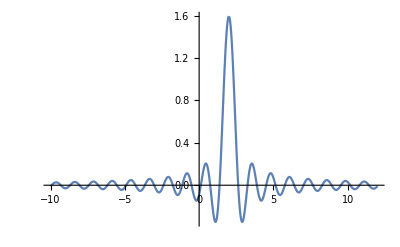

```mathematica
s[x_]:=Sin[g(x-a)]/(π(x-a));
Limit[s[x],x->0]
a=2;g=5;
Plot[s[x],{x,-10,10+a},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
S[x_,p_]:=Sin[p(x-b)]/(π(x-b));
Limit[S[x,p],x->0]
Limit[S[x,p],p->∞]
```

Sin[b p]/(b π)

ConditionalExpression[Indeterminate,-b+x∈ℝ]

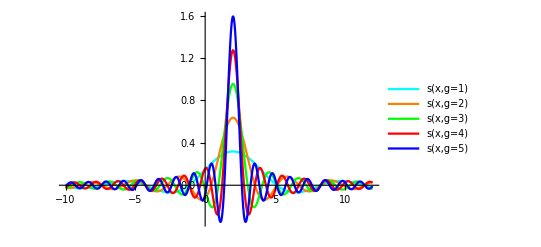

```mathematica
s[x_,g_]:=Sin[g(x-a)]/(π(x-a));
a=2;
Plot[{s[x,g=1],s[x,g=2],s[x,g=3],s[x,g=4],s[x,g=5]},{x,-10,10+a},PlotRange->Full,PlotStyle->{Cyan,Orange,Green,Red,Blue},PlotLegends->"Expressions"]
```

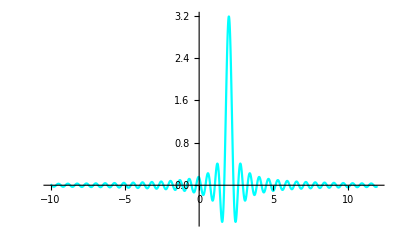

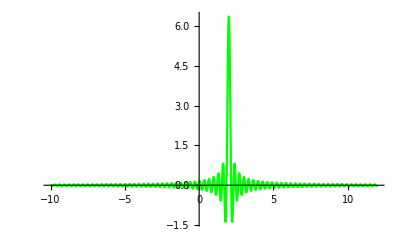

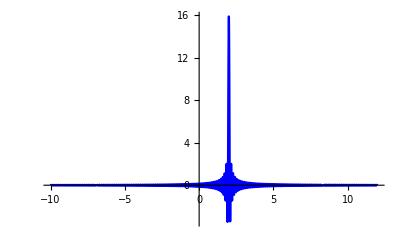

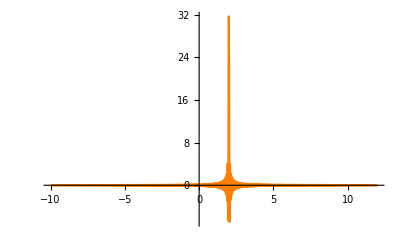

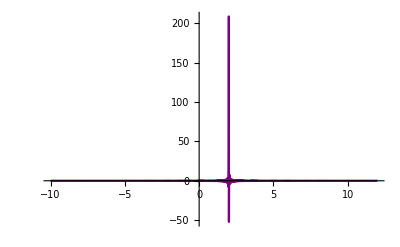

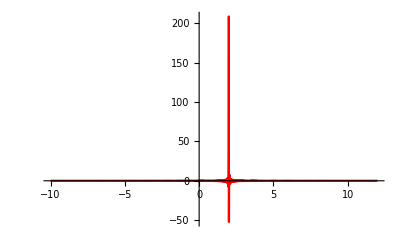

```mathematica
s[x_,g_]:=Sin[g(x-a)]/(π(x-a));
a=2;
Plot[s[x,g=10],{x,-10,10+a},PlotRange->Full,PlotStyle->Cyan,PlotLegends->"Expressions"]
Plot[s[x,g=20],{x,-10,10+a},PlotRange->Full,PlotStyle->Green]
Plot[s[x,g=50],{x,-10,10+a},PlotRange->Full,PlotStyle->Blue]
Plot[s[x,g=100],{x,-10,10+a},PlotRange->Full,PlotStyle->Orange]
Plot[s[x,g=1000],{x,-10,10+a},PlotRange->Full,PlotStyle->Purple]
Plot[s[x,g=1000],{x,-10,10+a},PlotRange->Full,PlotStyle->Red]
```

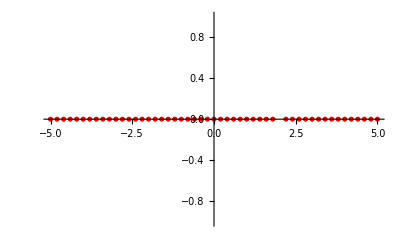

```mathematica
f[x_]:=DiracDelta[x-a];
a=2;
DiscretePlot[f[x],{x,-5,5,0.2},PlotStyle->{Red,Thick}]
```

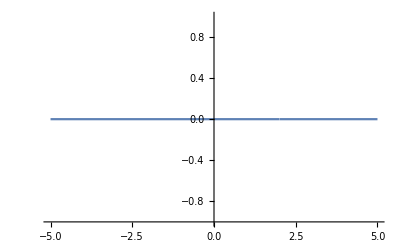

```mathematica
f[x_]:=DiracDelta[x-a];
a=2;
Plot[f[x],{x,-5,5},AxesOrigin->{0,-1}]
```

```mathematica
Exit
```

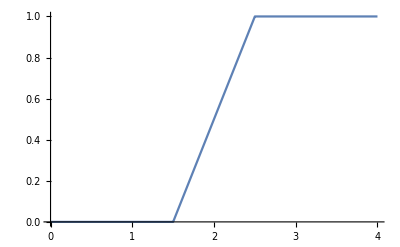

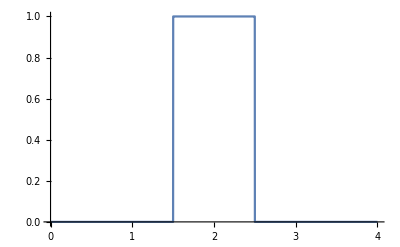

```mathematica
F[x_,σ_]:=Piecewise[{{0,x<a-σ},{(1/(2σ))(x-a+σ),-σ<x-a<σ},{1,x>a+σ}}]; (*Ramp function*)
der[x_,σ_]=D[F[x,σ],x];                                                                                                                                                           (*Derivative of Ramp function is Rectangular function R*)
a=2;
Plot[F[x,σ=0.5],{x,0,4},PlotRange->Full]
Plot[der[x,σ=0.5],{x,0,4},PlotRange->Full]
```

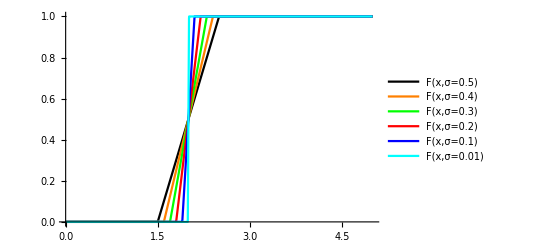

```mathematica
F[x_,σ_]:=Piecewise[{{0,x<a-σ},{(1/(2σ))(x-a+σ),-σ<x-a<σ},{1,x>a+σ}}];
a=2;
Plot[{F[x,σ=0.5],F[x,σ=0.4],F[x,σ=0.3],F[x,σ=0.2],F[x,σ=0.1],F[x,σ=0.01]},{x,0,5},PlotRange->Full,PlotStyle->{Black,Orange,Green,Red,Blue,Cyan},PlotLegends->"Expressions"]
```

```mathematica
Exit
```

```mathematica
F[x_,σ_]:=Piecewise[{{0,x<a-σ},{(1/(2σ))(x-a+σ),-σ<x-a<σ},{1,x>a+σ}}];
H[x_,a_]=Limit[F[x,σ],σ->0];                                                                                                                                                   (*For limit σ->0 Ramp function becomes Heaviside unit step function*)
H[x,a]
delta[x_,a_]=D[H[x,a],x];                                                                                                                                                           (*Derivative of dicontinuous Heaviside unit step function is Dirac delta function*)
delta[x,a]
Integrate[delta[x,a=2],{x,-5,5}]
```

Piecewise[{{1, x>2}, {0, x<2}, {Indeterminate, True}}]

Piecewise[{{0, x<2||x>2}, {Indeterminate, True}}]

0

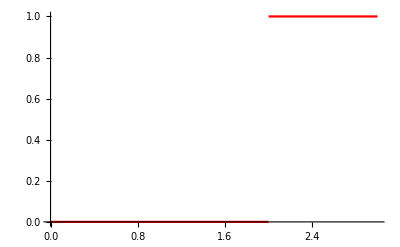

-Graphics-

```mathematica
a=2;
Plot[H[x,a],{x,0,3},PlotStyle->{Red,Thick},PlotLegends->"H(x-2):Heaviside unit step function,\ndiscontinuous function"]
DiscretePlot[delta[x,a],{x,-5,5,0.2},PlotStyle->{Red,Thick},PlotLegends->"δ(x-2): Dirac delta function"]
```

```mathematica
Plot[UnitStep[x-2],{x,0,3},PlotStyle->{Red,Thick},PlotLegends->"H(x-2):Heaviside unit step function"]
```

-Graphics-

```mathematica
Exit
```

Piecewise[{{ⅇ^x, x<0}, {-ⅇ^-x, x>0}, {Indeterminate, True}}]

Piecewise[{{ⅇ^x, x<0}, {ⅇ^-x, x>0}, {Indeterminate, True}}]

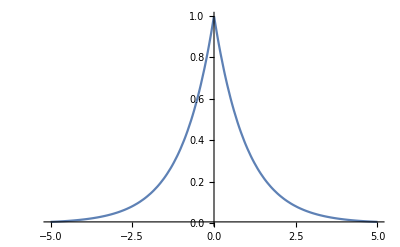

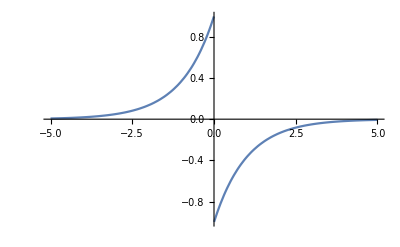

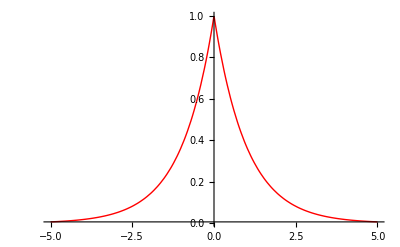

```mathematica
(*psi[x_]:=Exp[-Abs[x]];*)  
psi[x_]:=Piecewise[{{Exp[-(x)],x>=0},{Exp[-(-x)],x<0}}];   
derpsi[x_]=D[psi[x],x]   
derderpsi[x_]=D[derpsi[x],x]                                         
Plot[psi[x],{x,-5,5},PlotRange->Full]
Plot[derpsi[x],{x,-5,5},PlotRange->Full]
Plot[derderpsi[x],{x,-5,5},PlotRange->Full,PlotStyle->{Red,Thick}]
```

1/(1-z)+z/(1-z)^2

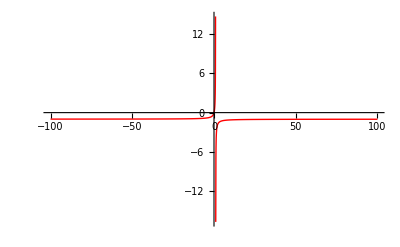

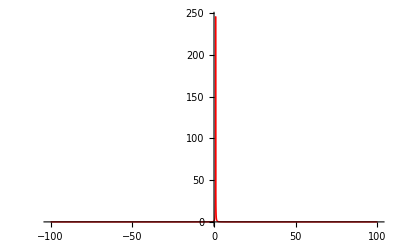

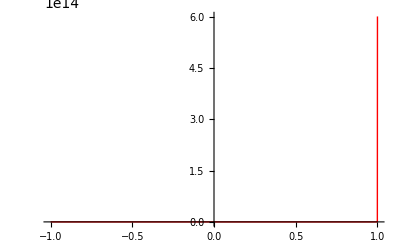

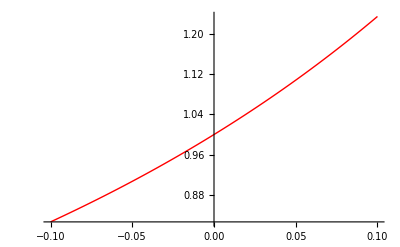

```mathematica
f[z_]:=z/(1-z);
der2[z_]=D[f[z],z]
Plot[f[z],{z,-100,100},PlotRange->Full,PlotStyle->{Red,Thick}]
Plot[der2[z],{z,-100,100},PlotRange->Full,PlotStyle->{Red,Thick}]
Plot[der2[z],{z,-1,1},PlotRange->Full,PlotStyle->{Red,Thick}]
Plot[der2[z],{z,-0.1,0.1},PlotRange->Full,PlotStyle->{Red,Thick}]
```

Piecewise[{{-1, x<0}, {1, x>0}, {Indeterminate, True}}]

Piecewise[{{0, x<0||x>0}, {Indeterminate, True}}]

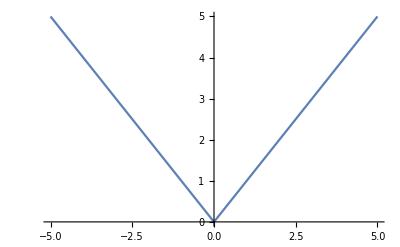

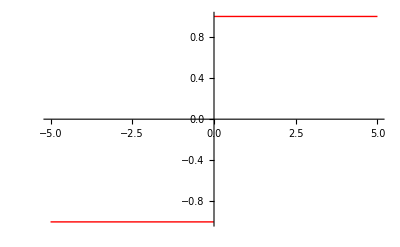

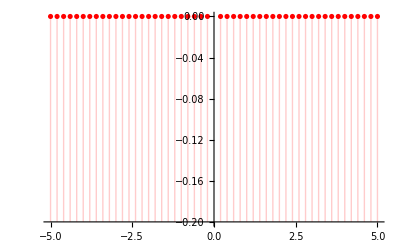

```mathematica
h[x_]:=Piecewise[{{-x,x<0},{x,x≥0}}];
derh[x_]=D[h[x],x]
derderh[x_]=D[derh[x],x]
Plot[h[x],{x,-5,5}]
Plot[derh[x],{x,-5,5},PlotRange->Full,PlotStyle->{Red,Thick}]
DiscretePlot[derderh[x],{x,-5,5,0.2},AxesOrigin->{0,-0.2},PlotRange->Full,PlotStyle->{Red,Thick}]
```

Piecewise[{{-1, x<2}, {1, x>2}, {Indeterminate, True}}]

Piecewise[{{0, x<2||x>2}, {Indeterminate, True}}]

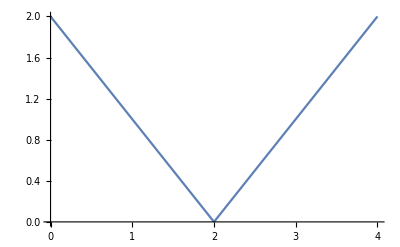

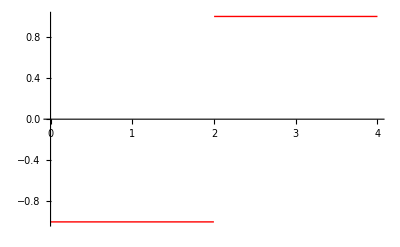

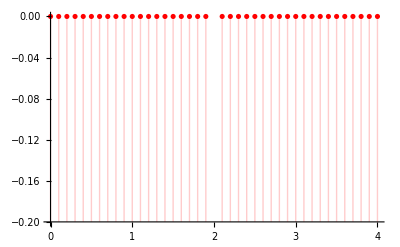

```mathematica
h[x_]:=Piecewise[{{-x+a,x<a},{x-a,x≥a}}];
a=2;
derh[x_]=D[h[x],x]
derderh[x_]=D[derh[x],x]
Plot[h[x],{x,0,4}]
Plot[derh[x],{x,0,4},PlotRange->Full,PlotStyle->{Red,Thick}]
DiscretePlot[derderh[x],{x,0,4,0.1},AxesOrigin->{0,-0.2},PlotRange->Full,PlotStyle->{Red,Thick}]
```

```mathematica
Exit
```

```mathematica
f[x_]:=x^2;
Integrate[f[x]DiracDelta[x-2],{x,-5,5}]
```

4

```mathematica
G3[x_,y_,z_]:=(1/((σ^3)*(2Pi)^(3/2)))Exp[-(((x-a)^2)+((y-b)^2)+((z-x)^2))/(2σ^2)];
a=2;b=3;c=2,σ=0.1;
ContourPlot3D[G3[x,y,z], {x, 0,5},{y,0,5},{z,0,5},PlotPoints->100,PlotRange->Full]
```